This notebook will be my attempt at modeling games by adversarial territory coloring

```mathematica
{{0.3, 0.3, 0.3}, {0.3, 0.3, 0.3}}
```

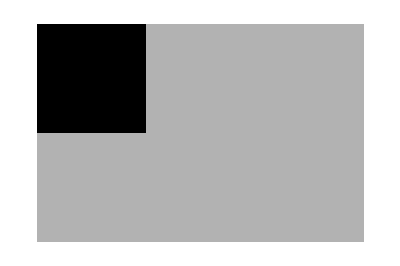

```mathematica
ArrayPlot[{{1,0.3,0.3},{0.3,0.3,0.3}}]
```



```mathematica
ArrayPlot[Table[0.3,{10}, {10}], ]
```

```mathematica
happy = ArrayPlot[{{Blue}}]
```

-Graphics-

```mathematica
unhappy = ArrayPlot[{{Red}}]
```

-Graphics-

```mathematica
whiterice = ArrayPlot[{{LightOrange}}]
```

-Graphics-

```mathematica
brownrice = ArrayPlot[{{Brown}}]
```

-Graphics-

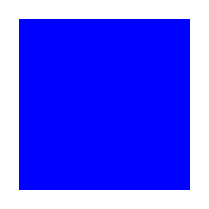

```mathematica
wellbeing[rice_] := If[rice == whiterice, happy, unhappy]
```

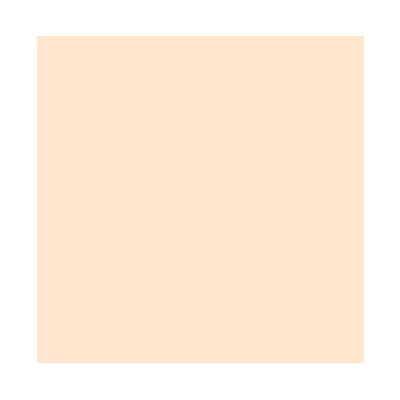
If[-Graphics-==-Graphics-,happy,unhappy]

```mathematica
wellbeing[-Graphics-]
```

People think that:
lifegoal = happiness
crutchlogic = Iff whiterice then willem will be happy
crutchlogic = True
If lifegoal == happiness and crutchlogic == True then spend money 
If whiterice 
If crutchlogic == False then whiterice is worth nothing
But really them thinking that is what causes it to be true
If willem believes crutchlogic  then crutchlogic = True else crutchlogic = False
wealth = revenue - expenses

I want to eat out because I enjoy the food, and it’s important to enjoy life.
 Let’s say, with all your bills paid you have an extra 500 to spend, and you spend 300 of that on going out to eat, and 200 you save every month. After a year you’ll have 2400 dollars saved up. It’s clear that you will never buy a house, be able to travel, or be able to support a family: Something has to change. So you say, I’m going to stop spending so much on going out to eat. You think, I do enjoy going out to eat, but it’s not worth it, the long term goals like buying a house are more important. You have some success the first day and you feel excited because your going to save up for a vacation to Ireland. Then a couple days go by, you get out of work, your tired and really want to treat yourself. So you say I’ll just chipotle this one time. 
 
Charlie Munger wrote in his book, “when solving a problem, invert, always invert.” Nassim Taleb’s version of this is “via negativa” improving things through removal rather than addition. I was watching an interview with Elon Musk about things he’s learned from Tesla and SpaceX. “The biggest mistake engineers make is they optimize a part that shouldn’t exist. The best part is no part, it costs nothing, it can’t break. There was a piece of glass in the model 3 that was holding up production, after pulling my hair out trying to optimize and automate this part, I finally asked, why do we need this damn thing! The fire safety team said that it was for soundproofing. The soundproofing team said it was for fire safety. So, they tested the sound and it was the same level of volume! Before you optimize you should always question your requirements because your requirements are almost always dumb.” This video of Elon Musk, with the towering Starship factory behind him, got me thinking about all the bullshit in my life that it was time to get rid of.

Allen Carr was a multi-pack-a-day smoker and created a method called Easyway to quit smoking. He went on to apply this method to a number of other addictions. I’d been meaning to cut out processed food from my diet for a while because I believed it was gonna make me die early, and harm my health. Pretty good incentives right, but despite believing this, I wasn’t able to stop eating chips, pasta and sugar. His book makes the almost magical claim that all it’s users have to do is read the book and they will be “cured” of their addiction, whatever it is: be it smoking, eating bad, etc. And he was right, ever since I read it, I only eat processed sugar when I have to. 
 
The way Easyway works is just by convincing you that all the reasons you tell yourself why you need processed food are bullshit. Once you believe that then it becomes easy to not eat processed food. There is the little monster, which is responsible for the slight almost imperceptible physical discomfort you get from not eating processed carbs. Then there is big monster, which is you telling yourself that you need to eat those foods, because “you like the taste” or “you had a bad day” or “life should be enjoyable”. If you can convince yourself you don’t need processed carbs to live a pleasurable life, then you’ll kill the big monster and will remove any desire for  processed carbs. 

 It’s not hard to then generalize from eating to anything. Replace “eating” with “any experience” and you get: The majority of the pleasure of experience doesn’t come from the physical sensations but from what you tell yourself about the experience. 

I’m repeatedly shocked by the power of the things I believe to alter my experience. I’ve long had the nasty habit of picking my nose in public. Even after reading Allen Carr’s book, I thought that my nose picking was just a habit and that the only way to change it was to provide some physical cue. I tried a fidget cube, finger sleeves, nothing worked.

I decided to try the Easyway for nose picking. I convinced myself that, “Picking my nose in the bathroom is just as pleasurable as picking my nose in public.” Once I whole-heartedly believed that, I knew I wouldn’t do it again and I haven’t since that day. 

One of the things I’ve been thinking about is, why does this work? Why do our beliefs have such a strong impact on our experience. I realized it’s rooted in the fact that our body is a complex system, with each part influencing the other parts. One of these pieces is our frontal lobe, where we form our beliefs. Our emotional brain, definitely has an effect on our reasoning brain, but it also goes the other way. Think about it, the emotional brain has to take the information available to it, and in response release the appropriate feeling for that situation. One very good piece of information it could use is our reasoning brain. If this giant computer up above me thinks that chips are going to make me happy, then they probably are. 

I also realized that this was not the first time I’ve heard of these ideas about the power of mindset. I had briefly read about stoic philosophy years ago. I revisited some of the stuff and found that the Easyway was really just stoicism. Epictetus puts it very simply:  “It’s not things that upset us but our judgments about things.” 

Applying the stoic idea to my finances, I realized that I don’t need to go out to eat that often. I can enjoy the cheap meals just as much as
the expensive ones, I just have to convince myself of the pleasure of a cheap meal. One way to get richer is to earn more. Another more subtle way, is to desire less. 

Let’s call an anti-stoic thought when you tell yourself you need something. This thought makes you fragile because it requires the world to give you that something for you to be happy. If you take anti-stoicism to the limit you get someone who tells themselves they need everything to be happy, which will by definition make them miserable. The kids I host birthdays for, often throw tantrums at the smallest bit of unpleasantness because it is their “special day”. 

If you take stoicism to the limit you get someone who is completely robust to any state of the world. Any thing you throw at him he can take it in stride. He doesn’t need shit from anyone, this is true freedom. 

So my advice to myself and others is this: Feel liberated in understanding that you are strong enough to handle any event, at any time, under any circumstance. Be cautious about carrying anti-stoic beliefs, they are toxic to a good life. Never treat yourself, and most of all,  avoid kids birthday parties.  

As always, thank you reader.

```mathematica
wealth = revenue - expenses
```

-expenses+revenue

```mathematica
Manipulate[revenue - expenses, {revenue, 0, 10, 1}, {expenses, 0, 10, 1}]
```

```mathematica
y = x - z
```

x-z

```mathematica
D[y, z]
```

-1

```mathematica
x-z
```

x-z

```mathematica
D[y, x]
```

1

```mathematica
D[y, x]
```

1

```mathematica
Manipulate[Plot[x-z,{x,-10,10}], {z, 0, 10, 1}]
```

```mathematica
Show[%127,ViewPoint->Front]
```

-Graphics3D-

```mathematica
Show[%118,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
Plot3D[y = x+z,{x,0,10}, {z, 0, 10} ]
```

Plot3D::argrx: Plot3D called with 2 arguments; 3 arguments are expected.

Plot3D[y=x+z,{{y,0,10},{x,0,10},{z,0,10}}]

```mathematica
Manipulate[Plot[Column[Table[$, revenue - spending]], {0,10}], {revenue, 0, 10, 1}, {spending, 0, 10, 1}]
```

Plot::pllim: Range specification {0,10} is not of the form {x, xmin, xmax}.

```mathematica
Import["/Users/erichegonzales/Projects/Wolfram/money_sign.jpg"]
```

-Graphics-

```mathematica
Manipulate[BarChart[{revenue - spending}, ChartElements -> -Graphics-, AxesOrigin->{0, 10}, BarSpacing->1], {revenue, 0, 10, 1}, {spending, 0, 10, 1}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Table::iterb: Iterator {System`BarFunctionDump`j,Ceiling[Abs[(System`BarFunctionDump`h)/0.]]} does not have appropriate bounds.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Table::iterb: Iterator {System`BarFunctionDump`j,Ceiling[Abs[(System`BarFunctionDump`h)/0.]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

```mathematica
ResourceFunction["DarkMode"][False]
```